# Analysis of CCE fish data

## Import and Curate Data

```mathematica
(* data in raw form (time, species, count) *)
raw=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transiitons_16/fish_project/data/data_CCE.csv"][[3;;,;;]];
```

```mathematica
raw//Dimensions
```

{328173,3}

```mathematica
(* extract date from time column *)
raw[[;;,1]]=StringTake[raw[[;;,1]],{1,10}];
```

```mathematica
(* make a function to convert date cell to number of days after 1951-01-08 *)
Clear[toDays]
SetAttributes[toDays,Listable]
toDays[date_]:=(DateObject[date]-DateObject[{1951,01,08}])//QuantityMagnitude
```

```mathematica
(* Tally time values, apply function to time values - put back into raw data *)
time=raw[[;;,1]];
temp=Tally[time];
timeVals=toDays[Tally[time][[;;,1]]];
newTime=Table[ConstantArray[timeVals[[i]],temp[[i,2]]],{i,1,Length[timeVals]}]//Flatten;
raw2=Prepend[Transpose[raw],newTime]//Transpose;
```

```mathematica
raw2[[1;;300,;;]]//MatrixForm
```

(1 | 1951-01-09 | Nannobrachium | 1
1 | 1951-01-09 | Sebastes | 1
1 | 1951-01-09 | Protomyctophum crockeri | 1
2 | 1951-01-10 | Protomyctophum crockeri | 2
2 | 1951-01-10 | Stenobrachius leucopsarus | 1
2 | 1951-01-10 | Vinciguerria lucetia | 4
2 | 1951-01-10 | Citharichthys | 1
2 | 1951-01-10 | Nannobrachium | 6
2 | 1951-01-10 | Sebastes | 6
2 | 1951-01-10 | Diogenichthys atlanticus | 2
2 | 1951-01-10 | Symbolophorus californiensis | 1
2 | 1951-01-10 | Trachurus symmetricus | 1
2 | 1951-01-10 | Cyclothone | 1
2 | 1951-01-10 | Vinciguerria lucetia | 13
2 | 1951-01-10 | Protomyctophum crockeri | 1
2 | 1951-01-10 | Unidentified | 1
2 | 1951-01-10 | Nannobrachium | 2
2 | 1951-01-10 | Stomias atriventer | 1
2 | 1951-01-10 | Tetragonurus cuvieri | 1
2 | 1951-01-10 | Vinciguerria lucetia | 1
2 | 1951-01-10 | Disintegrated fish larvae | 1
2 | 1951-01-10 | Symbolophorus californiensis | 2
2 | 1951-01-10 | Protomyctophum crockeri | 1
2 | 1951-01-10 | Bathylagoides wesethi | 2
2 | 1951-01-10 | Stenobrachius leucopsarus | 1
2 | 1951-01-10 | Myctophidae | 1
2 | 1951-01-11 | Bathylagoides wesethi | 2
2 | 1951-01-11 | Myctophum nitidulum | 1
2 | 1951-01-11 | Hygophum atratum | 1
2 | 1951-01-11 | Diogenichthys | 5
2 | 1951-01-11 | Ceratoscopelus townsendi | 1
2 | 1951-01-11 | Cyclothone | 3
2 | 1951-01-11 | Vinciguerria lucetia | 2
2 | 1951-01-11 | Symbolophorus californiensis | 2
2 | 1951-01-11 | Cyclothone | 4
2 | 1951-01-11 | Merluccius productus | 1
2 | 1951-01-11 | Tetragonurus cuvieri | 1
2 | 1951-01-11 | Nannobrachium | 6
2 | 1951-01-11 | Stenobrachius leucopsarus | 1
2 | 1951-01-11 | Idiacanthus antrostomus | 2
2 | 1951-01-11 | Diogenichthys atlanticus | 1
2 | 1951-01-11 | Paralepididae | 1
2 | 1951-01-11 | Cololabis saira | 1
2 | 1951-01-11 | Symbolophorus californiensis | 2
2 | 1951-01-11 | Symbolophorus californiensis | 1
2 | 1951-01-11 | Sebastes | 2
2 | 1951-01-11 | Idiacanthus antrostomus | 1
2 | 1951-01-11 | Unidentified | 1
2 | 1951-01-11 | Paralepididae | 1
2 | 1951-01-11 | Stenobrachius leucopsarus | 4
2 | 1951-01-11 | Protomyctophum crockeri | 2
3 | 1951-01-11 | Sebastes | 3
3 | 1951-01-11 | Melamphaes | 3
3 | 1951-01-11 | Stenobrachius leucopsarus | 10
3 | 1951-01-11 | Paralepididae | 1
3 | 1951-01-12 | Citharichthys | 1
3 | 1951-01-12 | Sebastes | 3
3 | 1951-01-13 | Protomyctophum crockeri | 1
3 | 1951-01-13 | Citharichthys | 2
3 | 1951-01-13 | Leuroglossus stilbius | 2
3 | 1951-01-13 | Engraulis mordax | 93
3 | 1951-01-13 | Sebastes | 22
3 | 1951-01-13 | Stenobrachius leucopsarus | 4
3 | 1951-01-13 | Nannobrachium | 1
3 | 1951-01-14 | Disintegrated fish larvae | 1
3 | 1951-01-14 | Sebastes | 3
3 | 1951-01-14 | Leuroglossus stilbius | 1
3 | 1951-01-14 | Stenobrachius leucopsarus | 1
3 | 1951-01-14 | Engraulis mordax | 1
3 | 1951-01-14 | Melamphaes | 1
3 | 1951-01-14 | Nannobrachium | 1
3 | 1951-01-14 | Sebastes | 2
3 | 1951-01-14 | Citharichthys | 1
3 | 1951-01-14 | Vinciguerria lucetia | 9
3 | 1951-01-14 | Brama | 1
3 | 1951-01-14 | Nannobrachium | 12
3 | 1951-01-14 | Leuroglossus stilbius | 1
3 | 1951-01-14 | Stenobrachius leucopsarus | 3
3 | 1951-01-14 | Cyclothone | 1
3 | 1951-01-14 | Symbolophorus californiensis | 1
3 | 1951-01-14 | Diogenichthys atlanticus | 1
3 | 1951-01-14 | Protomyctophum crockeri | 1
3 | 1951-01-14 | Lipolagus ochotensis | 1
3 | 1951-01-14 | Diogenichthys atlanticus | 1
3 | 1951-01-14 | Nannobrachium | 8
3 | 1951-01-14 | Cyclothone | 1
3 | 1951-01-14 | Ichthyococcus | 1
3 | 1951-01-14 | Melamphaes | 1
3 | 1951-01-14 | Paralepididae | 2
3 | 1951-01-14 | Symbolophorus californiensis | 1
3 | 1951-01-14 | Cololabis saira | 1
3 | 1951-01-15 | Myctophidae | 5
3 | 1951-01-15 | Tetragonurus cuvieri | 1
3 | 1951-01-15 | Brama | 2
3 | 1951-01-15 | Symbolophorus californiensis | 15
3 | 1951-01-15 | Bathylagoides wesethi | 1
3 | 1951-01-15 | Vinciguerria lucetia | 5
3 | 1951-01-15 | Cololabis saira | 1
3 | 1951-01-15 | Ceratoscopelus townsendi | 1
3 | 1951-01-15 | Electrona risso | 5
4 | 1951-01-15 | Diogenichthys atlanticus | 34
4 | 1951-01-15 | Cyclothone | 10
4 | 1951-01-15 | Unidentified | 4
4 | 1951-01-15 | Loweina rara | 1
4 | 1951-01-15 | Nannobrachium | 2
4 | 1951-01-15 | Vinciguerria lucetia | 6
4 | 1951-01-15 | Diogenichthys atlanticus | 6
4 | 1951-01-15 | Cololabis saira | 2
4 | 1951-01-15 | Cyclothone | 5
5 | 1951-01-15 | Hygophum reinhardtii | 3
5 | 1951-01-15 | Symbolophorus californiensis | 1
5 | 1951-01-15 | Nannobrachium | 1
5 | 1951-01-15 | Idiacanthus antrostomus | 1
5 | 1951-01-15 | Ceratoscopelus townsendi | 2
5 | 1951-01-15 | Protomyctophum crockeri | 1
5 | 1951-01-15 | Vinciguerria lucetia | 2
6 | 1951-01-15 | Cyclothone | 2
6 | 1951-01-16 | Loweina rara | 1
6 | 1951-01-16 | Stomias atriventer | 1
6 | 1951-01-16 | Ceratoscopelus townsendi | 5
6 | 1951-01-16 | Protomyctophum crockeri | 1
6 | 1951-01-16 | Hygophum reinhardtii | 1
6 | 1951-01-16 | Paralepididae | 1
6 | 1951-01-16 | Cyclothone | 1
6 | 1951-01-16 | Vinciguerria lucetia | 9
6 | 1951-01-16 | Symbolophorus californiensis | 1
6 | 1951-01-16 | Paralepididae | 1
6 | 1951-01-16 | Cyclothone | 1
6 | 1951-01-16 | Protomyctophum crockeri | 3
6 | 1951-01-16 | Diogenichthys atlanticus | 1
6 | 1951-01-16 | Stenobrachius leucopsarus | 1
6 | 1951-01-17 | Protomyctophum crockeri | 1
6 | 1951-01-17 | Ceratoscopelus townsendi | 1
6 | 1951-01-17 | Diogenichthys atlanticus | 2
6 | 1951-01-17 | Citharichthys | 1
6 | 1951-01-17 | Nannobrachium | 3
6 | 1951-01-17 | Cyclothone | 3
6 | 1951-01-17 | Nannobrachium | 1
6 | 1951-01-17 | Diogenichthys atlanticus | 1
6 | 1951-01-17 | Citharichthys | 1
6 | 1951-01-17 | Scopelarchidae | 1
6 | 1951-01-17 | Myctophidae | 1
6 | 1951-01-17 | Diogenichthys atlanticus | 8
6 | 1951-01-17 | Tetragonurus cuvieri | 1
6 | 1951-01-17 | Symbolophorus californiensis | 2
6 | 1951-01-17 | Sebastes | 13
6 | 1951-01-17 | Trachipteridae | 1
6 | 1951-01-17 | Sebastes goodei | 2
6 | 1951-01-17 | Sebastes paucispinis | 1
7 | 1951-01-17 | Pleuronichthys decurrens | 1
7 | 1951-01-18 | Protomyctophum crockeri | 2
7 | 1951-01-18 | Stenobrachius leucopsarus | 24
7 | 1951-01-18 | Sebastes paucispinis | 1
7 | 1951-01-18 | Lipolagus ochotensis | 2
7 | 1951-01-18 | Sebastes jordani | 1
7 | 1951-01-18 | Sebastes | 2
7 | 1951-01-18 | Engraulis mordax | 1
7 | 1951-01-18 | Leuroglossus stilbius | 4
7 | 1951-01-18 | Tarletonbeania crenularis | 1
7 | 1951-01-18 | Sebastes | 38
7 | 1951-01-18 | Stenobrachius leucopsarus | 3
7 | 1951-01-18 | Disintegrated fish larvae | 2
7 | 1951-01-18 | Unidentified | 1
7 | 1951-01-18 | Sebastes paucispinis | 4
7 | 1951-01-18 | Sebastes jordani | 2
7 | 1951-01-18 | Leuroglossus stilbius | 5
7 | 1951-01-18 | Citharichthys | 3
7 | 1951-01-18 | Engraulis mordax | 1
7 | 1951-01-18 | Engraulis mordax | 1
7 | 1951-01-18 | Pleuronichthys coenosus | 1
7 | 1951-01-18 | Gobiidae | 1
7 | 1951-01-18 | Sebastes | 27
7 | 1951-01-18 | Pleuronichthys decurrens | 1
7 | 1951-01-18 | Lipolagus ochotensis | 3
7 | 1951-01-18 | Leuroglossus stilbius | 34
7 | 1951-01-18 | Sebastes diploproa | 3
7 | 1951-01-18 | Sebastes paucispinis | 4
7 | 1951-01-18 | Tarletonbeania crenularis | 1
7 | 1951-01-18 | Stenobrachius leucopsarus | 61
7 | 1951-01-18 | Sebastes jordani | 2
7 | 1951-01-18 | Nannobrachium | 2
7 | 1951-01-18 | Sebastes | 10
7 | 1951-01-18 | Sebastes jordani | 17
7 | 1951-01-18 | Merluccius productus | 2
7 | 1951-01-18 | Sebastes paucispinis | 8
7 | 1951-01-18 | Leuroglossus stilbius | 69
7 | 1951-01-18 | Lipolagus ochotensis | 1
7 | 1951-01-18 | Stenobrachius leucopsarus | 39
7 | 1951-01-18 | Engraulis mordax | 27
8 | 1951-01-18 | Protomyctophum crockeri | 1
8 | 1951-01-19 | Sebastes | 3
8 | 1951-01-19 | Engraulis mordax | 12
8 | 1951-01-19 | Merluccius productus | 3
8 | 1951-01-19 | Stenobrachius leucopsarus | 55
8 | 1951-01-19 | Icichthys lockingtoni | 1
8 | 1951-01-19 | Leuroglossus stilbius | 69
8 | 1951-01-19 | Lipolagus ochotensis | 1
8 | 1951-01-19 | Sebastes jordani | 8
8 | 1951-01-19 | Sebastes paucispinis | 5
8 | 1951-01-19 | Sebastes aurora | 1
8 | 1951-01-19 | Leuroglossus stilbius | 25
8 | 1951-01-19 | Lipolagus ochotensis | 1
8 | 1951-01-19 | Sebastes paucispinis | 14
8 | 1951-01-19 | Sebastes jordani | 5
8 | 1951-01-19 | Tarletonbeania crenularis | 4
8 | 1951-01-19 | Stenobrachius leucopsarus | 209
8 | 1951-01-19 | Lyopsetta exilis | 1
8 | 1951-01-19 | Engraulis mordax | 13
8 | 1951-01-19 | Sebastes | 10
8 | 1951-01-19 | Citharichthys | 2
8 | 1951-01-19 | Nannobrachium | 1
8 | 1951-01-20 | Sebastes | 6
8 | 1951-01-20 | Stenobrachius leucopsarus | 26
8 | 1951-01-20 | Icichthys lockingtoni | 1
8 | 1951-01-20 | Leuroglossus stilbius | 129
8 | 1951-01-20 | Girella nigricans | 1
8 | 1951-01-20 | Sebastes diploproa | 3
8 | 1951-01-20 | Sternoptychidae | 1
8 | 1951-01-20 | Leuroglossus stilbius | 1
8 | 1951-01-20 | Protomyctophum crockeri | 1
8 | 1951-01-20 | Citharichthys | 1
9 | 1951-01-20 | Protomyctophum crockeri | 1
9 | 1951-01-21 | Myctophum nitidulum | 1
9 | 1951-01-21 | Diogenichthys laternatus | 1
9 | 1951-01-21 | Cololabis saira | 1
9 | 1951-01-21 | Diogenichthys | 1
9 | 1951-01-21 | Symbolophorus californiensis | 7
9 | 1951-01-21 | Cyclothone | 6
9 | 1951-01-21 | Nannobrachium | 2
9 | 1951-01-21 | Paralepididae | 2
9 | 1951-01-21 | Protomyctophum crockeri | 2
9 | 1951-01-21 | Stenobrachius leucopsarus | 1
9 | 1951-01-21 | Stomias atriventer | 1
9 | 1951-01-21 | Paralepididae | 1
9 | 1951-01-21 | Stenobrachius leucopsarus | 1
9 | 1951-01-21 | Protomyctophum crockeri | 1
9 | 1951-01-21 | Vinciguerria lucetia | 1
9 | 1951-01-21 | Symbolophorus californiensis | 2
9 | 1951-01-21 | Cyclothone | 4
9 | 1951-01-21 | Bathylagoides wesethi | 2
9 | 1951-01-21 | Diogenichthys | 4
9 | 1951-01-21 | Protomyctophum crockeri | 1
9 | 1951-01-21 | Nannobrachium | 3
9 | 1951-01-22 | Cololabis saira | 1
9 | 1951-01-22 | Diogenichthys | 1
9 | 1951-01-22 | Stenobrachius leucopsarus | 2
9 | 1951-01-22 | Symbolophorus californiensis | 1
9 | 1951-01-22 | Paralepididae | 1
9 | 1951-01-22 | Nannobrachium | 1
9 | 1951-01-22 | Melamphaes | 1
9 | 1951-01-22 | Paralepididae | 1
9 | 1951-01-22 | Stenobrachius leucopsarus | 1
9 | 1951-01-22 | Protomyctophum crockeri | 1
9 | 1951-01-22 | Sebastes | 6
9 | 1951-01-22 | Sebastes | 63
9 | 1951-01-22 | Disintegrated fish larvae | 1
9 | 1951-01-22 | Merluccius productus | 1
9 | 1951-01-22 | Stenobrachius leucopsarus | 5
9 | 1951-01-22 | Nannobrachium | 2
9 | 1951-01-23 | Gobiidae | 2
9 | 1951-01-23 | Sebastes | 80
9 | 1951-01-23 | Stenobrachius leucopsarus | 115
9 | 1951-01-23 | Engraulis mordax | 48
9 | 1951-01-23 | Citharichthys | 15
9 | 1951-01-23 | Merluccius productus | 1
9 | 1951-01-23 | Argentina sialis | 2
9 | 1951-01-23 | Nannobrachium | 1
9 | 1951-01-10 | Protomyctophum crockeri | 3
10 | 1951-01-10 | Citharichthys | 16
10 | 1951-01-10 | Argentina sialis | 3
10 | 1951-01-10 | Sebastes | 91
10 | 1951-01-10 | Engraulis mordax | 14
10 | 1951-01-10 | Argentina sialis | 3
10 | 1951-01-10 | Engraulis mordax | 67
10 | 1951-01-10 | Disintegrated fish larvae | 3
10 | 1951-01-10 | Unidentified | 2
10 | 1951-01-10 | Melamphaes | 2
10 | 1951-01-10 | Protomyctophum crockeri | 1
10 | 1951-01-10 | Nannobrachium | 1
10 | 1951-01-10 | Citharichthys | 72
10 | 1951-01-10 | Sebastes | 38
10 | 1951-01-10 | Engraulis mordax | 4
10 | 1951-01-10 | Paralepididae | 1
10 | 1951-01-10 | Nannobrachium | 1
10 | 1951-01-10 | Disintegrated fish larvae | 12
10 | 1951-01-10 | Triphoturus mexicanus | 1
10 | 1951-01-10 | Diogenichthys atlanticus | 2
10 | 1951-01-10 | Nannobrachium | 1
10 | 1951-01-10 | Diogenichthys laternatus | 3
10 | 1951-01-10 | Triphoturus mexicanus | 2
10 | 1951-01-10 | Protomyctophum crockeri | 1
10 | 1951-01-10 | Scopelarchidae | 1
10 | 1951-01-11 | Protomyctophum crockeri | 1
10 | 1951-01-11 | Citharichthys | 2
10 | 1951-01-11 | Vinciguerria lucetia | 5
10 | 1951-01-11 | Nannobrachium | 2
10 | 1951-01-11 | Diogenichthys laternatus | 2
10 | 1951-01-11 | Engraulis mordax | 3
10 | 1951-01-11 | Vinciguerria lucetia | 25
10 | 1951-01-11 | Nannobrachium | 2)

### Type of fish

```mathematica
(* list of exploited fish species *)
fishExp={"Engraulis mordax","Merluccius productus","Sardinops sagax","Scomber japonicus","Trachurus symmetricus","Microstomus pacificus" ,"Paralabrax clathratus","Paralichthys californicus","Parophrys vetulus","Scorpaenichthys marmoratus" ,"Sebastes aurora","Sebastes paucispinis", "Sphyraena argentea"};
```

```mathematica
fishNexp={"Cololabis saira","Icichthys lockingtoni","Leuroglossus stilbius","Tetragonurus cuvieri","Trachipterus altivelis","Chromis punctipinnis","Lyopsetta exilis","Hippoglossina stomata","Pleuronichthys verticalis","Sebastes jordani","Symphurus atricaudus","Zaniolepis frenata","Argentina sialis","Hypsoblennius jenkinsi","Ophidion scrippsae","Oxylebius pictus"};
```

```mathematica
(* organise data into fish types *)
```

#### Exploited Fish

```mathematica
exp1//Dimensions
```

{13}

```mathematica
exp1[[1]]
```

{{3,93},{3,1},{7,1},{7,1},{7,1},{7,27},{8,12},{8,13},{9,48},{10,14},{10,67},{10,4},{10,3},{10,3},{11,1},{12,11},18461,{23466,1},{23466,1},{23466,16},{23466,9},{23469,8},{23469,4},{23475,1},{23476,5},{23477,7},{23477,24},{23477,5},{23477,5},{23470,1},{23471,2},{23471,1},{23473,1}}
 |  |  |  |

```mathematica
exp1=Table[Cases[raw2,{_,_,fishExp[[i]],_}][[;;,{1,4}]],{i,1,Length[fishExp]}];
nexp1=Table[Cases[raw2,{_,_,fishNexp[[i]],_}][[;;,{1,4}]],{i,1,Length[fishNexp]}];
```

```mathematica
(* Size of bins (days) *)
binSize=100;
maxi=Floor[Last[timeVals]/binSize,binSize]
```

200

```mathematica
ConstantArray[0,{3,5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
exp1//Dimensions
```

{13}

```mathematica
(* j cycles through bins *)
binSize=1000;
tmax=Last[timeVals];
jmax=Floor[tmax/binSize];
expSeries=ConstantArray[0,{Length[fishExp],jmax}];
(* i cycles through time values of each bin *)
i=1;
j=1;
(* count for number of fish *)
count=0;
(* k counts over fish species *)
```

```mathematica
For[k=1,k≤Length[fishExp],k++,
For[j=1,j≤jmax,j++,
While[exp1[[k,i,1]]≤j*binSize&&i≤Dimensions[exp1[[k]]][[1]] ,
count=count+exp1[[k,i,2]];
i=i+1;
];
expSeries[[k,j]]=count;
count=0;];
i=1;
]
```

$Aborted

```mathematica
tBinSeries=Table[binSize*j,{j,1,jmax}];
```

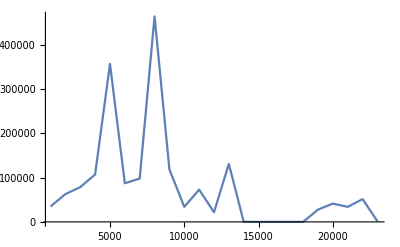
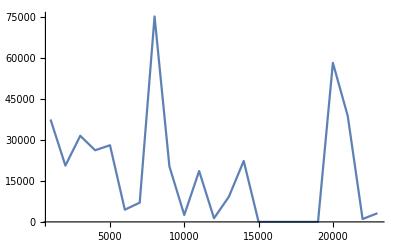
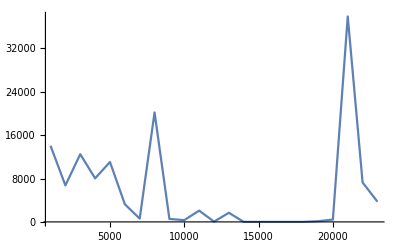
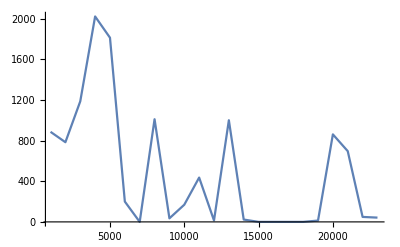
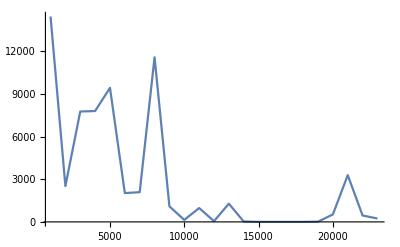
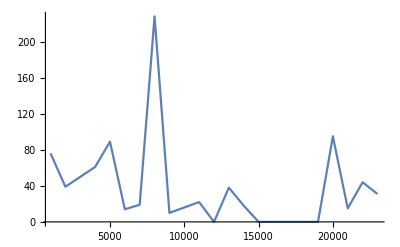
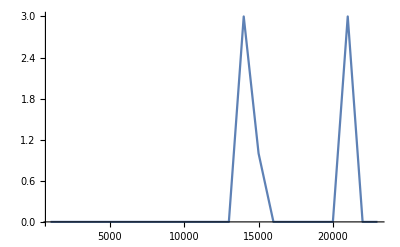
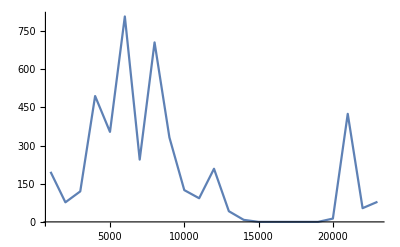

```mathematica
Table[ListLinePlot[Transpose[{tBinSeries,expSeries[[k]]}],PlotRange->All],{k,1,13}]
```